# Call Python to compute CY metrics

The easiest thing to get started would be to just run the entire notebook

In order to install the program, you just need to call Setup[] (Setup will detect whether you have run it before and not do anything if everything is already setup; so it does not hurt to just compile the entire notebook every time). Setup[] will try to discover python3 on your system and create a virtual environment with all required packages installed. For some combinations of Python and Mathematica versions, setup will automatically apply a bug fix. 

If you want to see the Documentation for any of the functions, run e.g. ?TrainNN. Running Options[TrainNN] gives you a list of the options for this function and their default values.

More advanced (if you do not want to just call Setup[] and be done with it):
1.)If you already have a python environment that you want to use, you need to “pip install --user pyzmq” for it to work with Mathematica.  
2.) Then setup the package to use this python interpreter with ChangeSetting[“Python”,”<path/to/python>”].

## Setup Python for CY metrics

Load the package for the web.
You can also download the package file and copy it to Mathematica’s Application folder. Too find the folder execute the following command in Mathematica: FileNameJoin[{$UserBaseDirectory,”/Applications”}] 
Then just copy the file https://github.com/pythoncymetric/cymetric/tree/main/cymetric/wolfram/cymetric.m to this directory and run with <<cymetric`

```mathematica
Get["https://raw.githubusercontent.com/pythoncymetric/cymetric/main/cymetric/wolfram/cymetric.m"];
```

```mathematica
(*Path where th virtual environment for python will be created. Defaults to the User's Desktop*)
PathToVenv=FileNameJoin[{$HomeDirectory,"Desktop/mathematica-venv"}];
(*If you already have an environment that you want to use, set the path here*)
(*ChangeSetting["Python","<path/to/python>"]*)
python=Setup[PathToVenv];
```

Mathematica discovered the following Python environments on your system:

Looking for Python 3

Found Python version 3.8.12 at /usr/local/bin/python3.8.

Creating virtual environment at /home/ruehle/Desktop/mathematica-venv

Upgrading pip...

Installing h5py...

Installing joblib...

Installing numpy...

Installing pyyaml...

Installing pyzmq...

Installing scipy...

Installing sympy...

Installing tensorflow==2.4.1...

Installing wolframclient...

Installing cymetric...

Registering venv with mathematica...

Checking whether 'externalevaluate.py' needs to be patched for this version...

Testing new environment...

Everything is working!

## Quintic

### Compute Points and Metric

To look at the parameters and options of a function, simply call ?<FunctionName> and Options[<FunctionName>]

```mathematica
?GeneratePoints
Options[GeneratePoints]
```

{KahlerModuli→{},Points→200000,Precision→20,VolJNorm→1,Python→Null,Session→Null,Dir→/home/ruehle/Desktop/test,Verbose→3}

Now we generate some points

```mathematica
outDir=FileNameJoin[{NotebookDirectory[],"Quintic"}];
```

```mathematica
poly={Subscript[z, 0]^5+Subscript[z, 1]^5+Subscript[z, 2]^5+Subscript[z, 3]^5+Subscript[z, 4]^5+10 Subscript[z, 0] Subscript[z, 1] Subscript[z, 2] Subscript[z, 3] Subscript[z, 4]};
{res,session}=GeneratePoints[poly,{4},"Points"->100000,"KahlerModuli"->{1},"Dir"->outDir,"VolJNorm"->5];
```

Warning: No variables specified, assuming alphabetical monomial ordering.

Variables have been assigned to the ambient space factors as follows:

1.) P^4: {z_0,z_1,z_2,z_3,z_4}

Generating 100000 points...

{x_(1,0)^5+x_(1,1)^5+x_(1,2)^5+x_(1,3)^5+10 x_(1,0) x_(1,1) x_(1,2) x_(1,3) x_(1,4)+x_(1,4)^5}

Configuration matrix: {{5}}

Number of Parameters per P^n: {1}

Number of points on CY from one ambient space intersection: 5

Now generating 100000 points...

done.

Writing points to /home/ruehle/Desktop/Quintic/points.pickle

DEBUG:mathematica:Using output directory /home/ruehle/Desktop/Quintic

DEBUG:mathematica:Ambient space: P^4

DEBUG:mathematica:Kahler moduli: [1]

DEBUG:mathematica:{'outdir': '/home/ruehle/Desktop/Quintic', 'logger_level': 10, 'num_pts': 100000, 'monomials': array([[[5, 0, 0, 0, 0],

[1, 1, 1, 1, 1],

[0, 5, 0, 0, 0],

[0, 0, 5, 0, 0],

[0, 0, 0, 5, 0],

[0, 0, 0, 0, 5]]]), 'coeffs': array([[ 1, 10, 1, 1, 1, 1]]), 'k_moduli': array([1]), 'ambient_dims': array([4]), 'precision': 20, 'vol_j_norm': 5, 'selected_t': array([1]), 'point_file_path': '/home/ruehle/Desktop/Quintic/points.pickle'}

INFO:mathematica:Saving point generator to /home/ruehle/Desktop/Quintic/point_gen.pickle

INFO:mathematica:Computing derivatives of J_FS, Omega, ...

DEBUG:mathematica:done

Now we train the NN (Training can be made faster if one sets “EvaluateModel”->False)

```mathematica
{history,session}=TrainNN["HiddenLayers"->{64,64,64},"ActivationFunctions"->{"gelu","gelu","gelu"},"Epochs"->100,"BatchSize"->64,"Session"->session,"EvaluateModel"->True,"Dir"->outDir,"Verbose"->3];
```

{
        'outdir':        "/home/ruehle/Desktop/Quintic",
        'logger_level':  logging.DEBUG,
        'model':         "MultFS",
        'callbacks':     True,
        'n_hiddens':     [64, 64, 64],
		'acts':          ["gelu", "gelu", "gelu"],
		'n_epochs':      100,
		'batch_size':    64,
		'kappa':         0.,
        'alphas':        [1., 1., 1., 1., 1.],
        'toric_data_path':""
       }

DEBUG:mathematica:Using CPU for computation.

DEBUG:mathematica:Model: "sequential"

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:Layer (type)                 Output Shape              Param #

DEBUG:mathematica:=================================================================

DEBUG:mathematica:dense (Dense)                (None, 64)                704

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_1 (Dense)              (None, 64)                4160

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_2 (Dense)              (None, 64)                4160

DEBUG:mathematica:_________________________________________________________________

DEBUG:mathematica:dense_3 (Dense)              (None, 9)                 585

DEBUG:mathematica:=================================================================

DEBUG:mathematica:Total params: 9,609

DEBUG:mathematica:Trainable params: 9,609

DEBUG:mathematica:Non-trainable params: 0

DEBUG:mathematica:_________________________________________________________________

- Sigma measure val:      0.2213

- Kaehler measure val:    0.0020

- Transition measure val: 0.0025

- Ricci measure val:      1.3289

- Volk val:               9.9308

Epoch 1/100

1407/1407 - 20s - sigma_loss: 0.2762 - kaehler_loss: 0.0051 - transition_loss: 0.0045 - volk_loss: 1.8501e-05

- Sigma measure val:      0.1326

- Kaehler measure val:    0.0019

- Transition measure val: 0.0052

- Ricci measure val:      0.2540

- Volk val:               0.9218

Epoch 2/100

1407/1407 - 7s - sigma_loss: 0.1311 - kaehler_loss: 0.0018 - transition_loss: 0.0055 - volk_loss: 1.6990e-05

- Sigma measure val:      0.1266

- Kaehler measure val:    0.0017

- Transition measure val: 0.0058

- Ricci measure val:      0.2348

- Volk val:               0.9438

Epoch 3/100

1407/1407 - 7s - sigma_loss: 0.1212 - kaehler_loss: 0.0028 - transition_loss: 0.0058 - volk_loss: 1.7068e-05

- Sigma measure val:      0.1202

- Kaehler measure val:    0.0047

- Transition measure val: 0.0052

- Ricci measure val:      0.2213

- Volk val:               0.9745

Epoch 4/100

1407/1407 - 7s - sigma_loss: 0.1122 - kaehler_loss: 0.0043 - transition_loss: 0.0037 - volk_loss: 1.7066e-05

- Sigma measure val:      0.1178

- Kaehler measure val:    0.0041

- Transition measure val: 0.0025

- Ricci measure val:      0.1638

- Volk val:               0.9139

Epoch 5/100

1407/1407 - 7s - sigma_loss: 0.1071 - kaehler_loss: 0.0035 - transition_loss: 0.0019 - volk_loss: 1.7170e-05

- Sigma measure val:      0.1109

- Kaehler measure val:    0.0036

- Transition measure val: 0.0016

- Ricci measure val:      0.1668

- Volk val:               1.0005

Epoch 6/100

1407/1407 - 7s - sigma_loss: 0.1056 - kaehler_loss: 0.0033 - transition_loss: 0.0016 - volk_loss: 1.7254e-05

- Sigma measure val:      0.1167

- Kaehler measure val:    0.0045

- Transition measure val: 0.0017

- Ricci measure val:      0.1806

- Volk val:               0.9578

Epoch 7/100

1407/1407 - 7s - sigma_loss: 0.1044 - kaehler_loss: 0.0034 - transition_loss: 0.0015 - volk_loss: 1.7223e-05

- Sigma measure val:      0.1105

- Kaehler measure val:    0.0030

- Transition measure val: 0.0014

- Ricci measure val:      0.1439

- Volk val:               0.9383

Epoch 8/100

1407/1407 - 7s - sigma_loss: 0.1034 - kaehler_loss: 0.0033 - transition_loss: 0.0015 - volk_loss: 1.7255e-05

- Sigma measure val:      0.1141

- Kaehler measure val:    0.0041

- Transition measure val: 0.0016

- Ricci measure val:      0.1690

- Volk val:               0.9437

Epoch 9/100

1407/1407 - 7s - sigma_loss: 0.1023 - kaehler_loss: 0.0033 - transition_loss: 0.0015 - volk_loss: 1.7210e-05

- Sigma measure val:      0.1105

- Kaehler measure val:    0.0033

- Transition measure val: 0.0015

- Ricci measure val:      0.1477

- Volk val:               0.9482

Epoch 10/100

1407/1407 - 7s - sigma_loss: 0.1019 - kaehler_loss: 0.0033 - transition_loss: 0.0015 - volk_loss: 1.7246e-05

- Sigma measure val:      0.1104

- Kaehler measure val:    0.0034

- Transition measure val: 0.0016

- Ricci measure val:      0.1620

- Volk val:               0.9709

Epoch 11/100

1407/1407 - 7s - sigma_loss: 0.1013 - kaehler_loss: 0.0033 - transition_loss: 0.0015 - volk_loss: 1.7244e-05

- Sigma measure val:      0.1117

- Kaehler measure val:    0.0032

- Transition measure val: 0.0016

- Ricci measure val:      0.1581

- Volk val:               0.9786

Epoch 12/100

1407/1407 - 7s - sigma_loss: 0.1001 - kaehler_loss: 0.0033 - transition_loss: 0.0016 - volk_loss: 1.7220e-05

- Sigma measure val:      0.1090

- Kaehler measure val:    0.0031

- Transition measure val: 0.0016

- Ricci measure val:      0.1402

- Volk val:               0.9125

Epoch 13/100

1407/1407 - 7s - sigma_loss: 0.0992 - kaehler_loss: 0.0032 - transition_loss: 0.0017 - volk_loss: 1.7223e-05

- Sigma measure val:      0.1094

- Kaehler measure val:    0.0034

- Transition measure val: 0.0017

- Ricci measure val:      0.1488

- Volk val:               0.9256

Epoch 14/100

1407/1407 - 7s - sigma_loss: 0.0966 - kaehler_loss: 0.0033 - transition_loss: 0.0018 - volk_loss: 1.7182e-05

- Sigma measure val:      0.1063

- Kaehler measure val:    0.0035

- Transition measure val: 0.0019

- Ricci measure val:      0.1432

- Volk val:               0.9291

Epoch 15/100

1407/1407 - 7s - sigma_loss: 0.0944 - kaehler_loss: 0.0033 - transition_loss: 0.0020 - volk_loss: 1.7051e-05

- Sigma measure val:      0.1008

- Kaehler measure val:    0.0032

- Transition measure val: 0.0020

- Ricci measure val:      0.1451

- Volk val:               0.9616

Epoch 16/100

1407/1407 - 7s - sigma_loss: 0.0911 - kaehler_loss: 0.0033 - transition_loss: 0.0021 - volk_loss: 1.6962e-05

- Sigma measure val:      0.1015

- Kaehler measure val:    0.0034

- Transition measure val: 0.0020

- Ricci measure val:      0.1378

- Volk val:               0.9905

Epoch 17/100

1407/1407 - 7s - sigma_loss: 0.0888 - kaehler_loss: 0.0033 - transition_loss: 0.0021 - volk_loss: 1.6868e-05

- Sigma measure val:      0.0979

- Kaehler measure val:    0.0032

- Transition measure val: 0.0020

- Ricci measure val:      0.1372

- Volk val:               0.9945

Epoch 18/100

1407/1407 - 7s - sigma_loss: 0.0874 - kaehler_loss: 0.0031 - transition_loss: 0.0020 - volk_loss: 1.6823e-05

- Sigma measure val:      0.0994

- Kaehler measure val:    0.0031

- Transition measure val: 0.0020

- Ricci measure val:      0.1556

- Volk val:               0.9678

Epoch 19/100

1407/1407 - 7s - sigma_loss: 0.0853 - kaehler_loss: 0.0028 - transition_loss: 0.0019 - volk_loss: 1.6799e-05

- Sigma measure val:      0.0946

- Kaehler measure val:    0.0027

- Transition measure val: 0.0018

- Ricci measure val:      0.1201

- Volk val:               0.9728

Epoch 20/100

1407/1407 - 7s - sigma_loss: 0.0826 - kaehler_loss: 0.0025 - transition_loss: 0.0018 - volk_loss: 1.6742e-05

- Sigma measure val:      0.0923

- Kaehler measure val:    0.0022

- Transition measure val: 0.0017

- Ricci measure val:      0.1112

- Volk val:               0.9736

Epoch 21/100

1407/1407 - 7s - sigma_loss: 0.0801 - kaehler_loss: 0.0022 - transition_loss: 0.0017 - volk_loss: 1.6668e-05

- Sigma measure val:      0.0923

- Kaehler measure val:    0.0019

- Transition measure val: 0.0015

- Ricci measure val:      0.0998

- Volk val:               0.9261

Epoch 22/100

1407/1407 - 7s - sigma_loss: 0.0767 - kaehler_loss: 0.0019 - transition_loss: 0.0015 - volk_loss: 1.6641e-05

- Sigma measure val:      0.0835

- Kaehler measure val:    0.0018

- Transition measure val: 0.0015

- Ricci measure val:      0.1068

- Volk val:               0.9379

Epoch 23/100

1407/1407 - 7s - sigma_loss: 0.0740 - kaehler_loss: 0.0018 - transition_loss: 0.0015 - volk_loss: 1.6545e-05

- Sigma measure val:      0.0807

- Kaehler measure val:    0.0017

- Transition measure val: 0.0014

- Ricci measure val:      0.0953

- Volk val:               0.9961

Epoch 24/100

1407/1407 - 7s - sigma_loss: 0.0712 - kaehler_loss: 0.0017 - transition_loss: 0.0015 - volk_loss: 1.6473e-05

- Sigma measure val:      0.0782

- Kaehler measure val:    0.0017

- Transition measure val: 0.0014

- Ricci measure val:      0.0936

- Volk val:               0.9679

Epoch 25/100

1407/1407 - 7s - sigma_loss: 0.0691 - kaehler_loss: 0.0017 - transition_loss: 0.0014 - volk_loss: 1.6435e-05

- Sigma measure val:      0.0782

- Kaehler measure val:    0.0017

- Transition measure val: 0.0014

- Ricci measure val:      0.1032

- Volk val:               1.0099

Epoch 26/100

1407/1407 - 7s - sigma_loss: 0.0671 - kaehler_loss: 0.0016 - transition_loss: 0.0014 - volk_loss: 1.6398e-05

- Sigma measure val:      0.0745

- Kaehler measure val:    0.0015

- Transition measure val: 0.0013

- Ricci measure val:      0.0764

- Volk val:               0.9451

Epoch 27/100

1407/1407 - 7s - sigma_loss: 0.0655 - kaehler_loss: 0.0015 - transition_loss: 0.0013 - volk_loss: 1.6356e-05

- Sigma measure val:      0.0724

- Kaehler measure val:    0.0015

- Transition measure val: 0.0013

- Ricci measure val:      0.0985

- Volk val:               0.9855

Epoch 28/100

1407/1407 - 7s - sigma_loss: 0.0644 - kaehler_loss: 0.0015 - transition_loss: 0.0012 - volk_loss: 1.6347e-05

- Sigma measure val:      0.0729

- Kaehler measure val:    0.0014

- Transition measure val: 0.0012

- Ricci measure val:      0.0849

- Volk val:               0.9858

Epoch 29/100

1407/1407 - 7s - sigma_loss: 0.0631 - kaehler_loss: 0.0014 - transition_loss: 0.0012 - volk_loss: 1.6339e-05

- Sigma measure val:      0.0744

- Kaehler measure val:    0.0013

- Transition measure val: 0.0011

- Ricci measure val:      0.0733

- Volk val:               0.9372

Epoch 30/100

1407/1407 - 7s - sigma_loss: 0.0627 - kaehler_loss: 0.0014 - transition_loss: 0.0012 - volk_loss: 1.6315e-05

- Sigma measure val:      0.0695

- Kaehler measure val:    0.0014

- Transition measure val: 0.0011

- Ricci measure val:      0.0814

- Volk val:               0.9632

Epoch 31/100

1407/1407 - 7s - sigma_loss: 0.0614 - kaehler_loss: 0.0014 - transition_loss: 0.0011 - volk_loss: 1.6341e-05

- Sigma measure val:      0.0682

- Kaehler measure val:    0.0014

- Transition measure val: 0.0011

- Ricci measure val:      0.0789

- Volk val:               0.9816

Epoch 32/100

1407/1407 - 7s - sigma_loss: 0.0610 - kaehler_loss: 0.0014 - transition_loss: 0.0011 - volk_loss: 1.6288e-05

- Sigma measure val:      0.0679

- Kaehler measure val:    0.0014

- Transition measure val: 0.0011

- Ricci measure val:      0.0819

- Volk val:               0.9810

Epoch 33/100

1407/1407 - 7s - sigma_loss: 0.0600 - kaehler_loss: 0.0013 - transition_loss: 0.0011 - volk_loss: 1.6301e-05

- Sigma measure val:      0.0685

- Kaehler measure val:    0.0014

- Transition measure val: 0.0010

- Ricci measure val:      0.0840

- Volk val:               0.9735

Epoch 34/100

1407/1407 - 7s - sigma_loss: 0.0595 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6285e-05

- Sigma measure val:      0.0676

- Kaehler measure val:    0.0014

- Transition measure val: 0.0010

- Ricci measure val:      0.0771

- Volk val:               0.9725

Epoch 35/100

1407/1407 - 7s - sigma_loss: 0.0590 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6293e-05

- Sigma measure val:      0.0680

- Kaehler measure val:    0.0013

- Transition measure val: 0.0010

- Ricci measure val:      0.0755

- Volk val:               0.9761

Epoch 36/100

1407/1407 - 7s - sigma_loss: 0.0587 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6261e-05

- Sigma measure val:      0.0662

- Kaehler measure val:    0.0012

- Transition measure val: 9.5563e-04

- Ricci measure val:      0.0699

- Volk val:               0.9408

Epoch 37/100

1407/1407 - 7s - sigma_loss: 0.0583 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6262e-05

- Sigma measure val:      0.0655

- Kaehler measure val:    0.0013

- Transition measure val: 0.0010

- Ricci measure val:      0.0771

- Volk val:               0.9733

Epoch 38/100

1407/1407 - 7s - sigma_loss: 0.0577 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6249e-05

- Sigma measure val:      0.0669

- Kaehler measure val:    0.0013

- Transition measure val: 0.0010

- Ricci measure val:      0.0717

- Volk val:               0.9582

Epoch 39/100

1407/1407 - 7s - sigma_loss: 0.0578 - kaehler_loss: 0.0013 - transition_loss: 9.9896e-04 - volk_loss: 1.6255e-05

- Sigma measure val:      0.0656

- Kaehler measure val:    0.0013

- Transition measure val: 9.8916e-04

- Ricci measure val:      0.0798

- Volk val:               1.0029

Epoch 40/100

1407/1407 - 7s - sigma_loss: 0.0572 - kaehler_loss: 0.0013 - transition_loss: 9.9099e-04 - volk_loss: 1.6263e-05

- Sigma measure val:      0.0669

- Kaehler measure val:    0.0012

- Transition measure val: 9.8286e-04

- Ricci measure val:      0.0755

- Volk val:               0.9981

Epoch 41/100

1407/1407 - 7s - sigma_loss: 0.0570 - kaehler_loss: 0.0013 - transition_loss: 9.8631e-04 - volk_loss: 1.6236e-05

- Sigma measure val:      0.0655

- Kaehler measure val:    0.0012

- Transition measure val: 9.9450e-04

- Ricci measure val:      0.0762

- Volk val:               0.9908

Epoch 42/100

1407/1407 - 7s - sigma_loss: 0.0565 - kaehler_loss: 0.0013 - transition_loss: 9.8939e-04 - volk_loss: 1.6237e-05

- Sigma measure val:      0.0674

- Kaehler measure val:    0.0012

- Transition measure val: 9.2978e-04

- Ricci measure val:      0.0709

- Volk val:               0.9930

Epoch 43/100

1407/1407 - 7s - sigma_loss: 0.0565 - kaehler_loss: 0.0013 - transition_loss: 9.9207e-04 - volk_loss: 1.6255e-05

- Sigma measure val:      0.0670

- Kaehler measure val:    0.0012

- Transition measure val: 9.4505e-04

- Ricci measure val:      0.0729

- Volk val:               0.9971

Epoch 44/100

1407/1407 - 7s - sigma_loss: 0.0560 - kaehler_loss: 0.0013 - transition_loss: 9.9412e-04 - volk_loss: 1.6258e-05

- Sigma measure val:      0.0627

- Kaehler measure val:    0.0013

- Transition measure val: 9.6527e-04

- Ricci measure val:      0.0710

- Volk val:               0.9775

Epoch 45/100

1407/1407 - 7s - sigma_loss: 0.0555 - kaehler_loss: 0.0013 - transition_loss: 9.9186e-04 - volk_loss: 1.6234e-05

- Sigma measure val:      0.0631

- Kaehler measure val:    0.0013

- Transition measure val: 0.0010

- Ricci measure val:      0.0762

- Volk val:               0.9824

Epoch 46/100

1407/1407 - 7s - sigma_loss: 0.0552 - kaehler_loss: 0.0013 - transition_loss: 9.9442e-04 - volk_loss: 1.6218e-05

- Sigma measure val:      0.0612

- Kaehler measure val:    0.0013

- Transition measure val: 9.8421e-04

- Ricci measure val:      0.0761

- Volk val:               0.9858

Epoch 47/100

1407/1407 - 7s - sigma_loss: 0.0552 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6202e-05

- Sigma measure val:      0.0619

- Kaehler measure val:    0.0013

- Transition measure val: 9.9788e-04

- Ricci measure val:      0.0709

- Volk val:               0.9707

Epoch 48/100

1407/1407 - 7s - sigma_loss: 0.0550 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6216e-05

- Sigma measure val:      0.0598

- Kaehler measure val:    0.0014

- Transition measure val: 0.0010

- Ricci measure val:      0.0785

- Volk val:               0.9948

Epoch 49/100

1407/1407 - 7s - sigma_loss: 0.0542 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6224e-05

- Sigma measure val:      0.0616

- Kaehler measure val:    0.0014

- Transition measure val: 0.0010

- Ricci measure val:      0.0670

- Volk val:               0.9468

Epoch 50/100

1407/1407 - 7s - sigma_loss: 0.0539 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6222e-05

- Sigma measure val:      0.0608

- Kaehler measure val:    0.0013

- Transition measure val: 0.0010

- Ricci measure val:      0.0753

- Volk val:               1.0014

Epoch 51/100

1407/1407 - 7s - sigma_loss: 0.0537 - kaehler_loss: 0.0013 - transition_loss: 0.0010 - volk_loss: 1.6206e-05

- Sigma measure val:      0.0589

- Kaehler measure val:    0.0013

- Transition measure val: 0.0010

- Ricci measure val:      0.0705

- Volk val:               0.9687

Epoch 52/100

1407/1407 - 7s - sigma_loss: 0.0532 - kaehler_loss: 0.0014 - transition_loss: 0.0010 - volk_loss: 1.6182e-05

- Sigma measure val:      0.0602

- Kaehler measure val:    0.0013

- Transition measure val: 0.0011

- Ricci measure val:      0.0756

- Volk val:               0.9853

Epoch 53/100

1407/1407 - 7s - sigma_loss: 0.0528 - kaehler_loss: 0.0014 - transition_loss: 0.0010 - volk_loss: 1.6176e-05

- Sigma measure val:      0.0609

- Kaehler measure val:    0.0013

- Transition measure val: 0.0010

- Ricci measure val:      0.0691

- Volk val:               0.9825

Epoch 54/100

1407/1407 - 7s - sigma_loss: 0.0525 - kaehler_loss: 0.0014 - transition_loss: 0.0011 - volk_loss: 1.6150e-05

- Sigma measure val:      0.0597

- Kaehler measure val:    0.0014

- Transition measure val: 0.0010

- Ricci measure val:      0.0709

- Volk val:               0.9777

Epoch 55/100

1407/1407 - 7s - sigma_loss: 0.0517 - kaehler_loss: 0.0014 - transition_loss: 0.0011 - volk_loss: 1.6164e-05

- Sigma measure val:      0.0586

- Kaehler measure val:    0.0014

- Transition measure val: 0.0011

- Ricci measure val:      0.0745

- Volk val:               0.9866

Epoch 56/100

1407/1407 - 7s - sigma_loss: 0.0509 - kaehler_loss: 0.0014 - transition_loss: 0.0011 - volk_loss: 1.6163e-05

- Sigma measure val:      0.0585

- Kaehler measure val:    0.0014

- Transition measure val: 0.0011

- Ricci measure val:      0.0708

- Volk val:               0.9935

Epoch 57/100

1407/1407 - 7s - sigma_loss: 0.0503 - kaehler_loss: 0.0015 - transition_loss: 0.0011 - volk_loss: 1.6160e-05

- Sigma measure val:      0.0565

- Kaehler measure val:    0.0014

- Transition measure val: 0.0011

- Ricci measure val:      0.0779

- Volk val:               1.0077

Epoch 58/100

1407/1407 - 7s - sigma_loss: 0.0496 - kaehler_loss: 0.0015 - transition_loss: 0.0011 - volk_loss: 1.6155e-05

- Sigma measure val:      0.0553

- Kaehler measure val:    0.0016

- Transition measure val: 0.0011

- Ricci measure val:      0.0728

- Volk val:               0.9848

Epoch 59/100

1407/1407 - 7s - sigma_loss: 0.0485 - kaehler_loss: 0.0016 - transition_loss: 0.0012 - volk_loss: 1.6125e-05

- Sigma measure val:      0.0542

- Kaehler measure val:    0.0015

- Transition measure val: 0.0012

- Ricci measure val:      0.0740

- Volk val:               0.9935

Epoch 60/100

1407/1407 - 7s - sigma_loss: 0.0479 - kaehler_loss: 0.0016 - transition_loss: 0.0012 - volk_loss: 1.6110e-05

- Sigma measure val:      0.0543

- Kaehler measure val:    0.0016

- Transition measure val: 0.0011

- Ricci measure val:      0.0726

- Volk val:               0.9906

Epoch 61/100

1407/1407 - 7s - sigma_loss: 0.0463 - kaehler_loss: 0.0017 - transition_loss: 0.0012 - volk_loss: 1.6097e-05

- Sigma measure val:      0.0512

- Kaehler measure val:    0.0018

- Transition measure val: 0.0012

- Ricci measure val:      0.0695

- Volk val:               0.9724

Epoch 62/100

1407/1407 - 7s - sigma_loss: 0.0450 - kaehler_loss: 0.0018 - transition_loss: 0.0012 - volk_loss: 1.6066e-05

- Sigma measure val:      0.0488

- Kaehler measure val:    0.0020

- Transition measure val: 0.0012

- Ricci measure val:      0.0714

- Volk val:               0.9614

Epoch 63/100

1407/1407 - 7s - sigma_loss: 0.0433 - kaehler_loss: 0.0019 - transition_loss: 0.0012 - volk_loss: 1.6048e-05

- Sigma measure val:      0.0453

- Kaehler measure val:    0.0018

- Transition measure val: 0.0012

- Ricci measure val:      0.0747

- Volk val:               0.9848

Epoch 64/100

1407/1407 - 7s - sigma_loss: 0.0416 - kaehler_loss: 0.0019 - transition_loss: 0.0012 - volk_loss: 1.6031e-05

- Sigma measure val:      0.0476

- Kaehler measure val:    0.0020

- Transition measure val: 0.0012

- Ricci measure val:      0.0726

- Volk val:               0.9870

Epoch 65/100

1407/1407 - 7s - sigma_loss: 0.0395 - kaehler_loss: 0.0020 - transition_loss: 0.0012 - volk_loss: 1.6007e-05

- Sigma measure val:      0.0423

- Kaehler measure val:    0.0020

- Transition measure val: 0.0012

- Ricci measure val:      0.0711

- Volk val:               0.9991

Epoch 66/100

1407/1407 - 7s - sigma_loss: 0.0379 - kaehler_loss: 0.0020 - transition_loss: 0.0012 - volk_loss: 1.5975e-05

- Sigma measure val:      0.0390

- Kaehler measure val:    0.0020

- Transition measure val: 0.0012

- Ricci measure val:      0.0745

- Volk val:               0.9990

Epoch 67/100

1407/1407 - 7s - sigma_loss: 0.0359 - kaehler_loss: 0.0021 - transition_loss: 0.0012 - volk_loss: 1.5964e-05

- Sigma measure val:      0.0351

- Kaehler measure val:    0.0020

- Transition measure val: 0.0012

- Ricci measure val:      0.0723

- Volk val:               0.9948

Epoch 68/100

1407/1407 - 7s - sigma_loss: 0.0342 - kaehler_loss: 0.0021 - transition_loss: 0.0012 - volk_loss: 1.5957e-05

- Sigma measure val:      0.0348

- Kaehler measure val:    0.0022

- Transition measure val: 0.0011

- Ricci measure val:      0.0676

- Volk val:               1.0078

Epoch 69/100

1407/1407 - 7s - sigma_loss: 0.0330 - kaehler_loss: 0.0021 - transition_loss: 0.0011 - volk_loss: 1.5952e-05

- Sigma measure val:      0.0326

- Kaehler measure val:    0.0020

- Transition measure val: 0.0011

- Ricci measure val:      0.0688

- Volk val:               0.9963

Epoch 70/100

1407/1407 - 7s - sigma_loss: 0.0317 - kaehler_loss: 0.0021 - transition_loss: 0.0011 - volk_loss: 1.5936e-05

- Sigma measure val:      0.0358

- Kaehler measure val:    0.0020

- Transition measure val: 0.0011

- Ricci measure val:      0.0583

- Volk val:               0.9729

Epoch 71/100

1407/1407 - 7s - sigma_loss: 0.0310 - kaehler_loss: 0.0020 - transition_loss: 0.0011 - volk_loss: 1.5924e-05

- Sigma measure val:      0.0330

- Kaehler measure val:    0.0020

- Transition measure val: 0.0011

- Ricci measure val:      0.0690

- Volk val:               1.0132

Epoch 72/100

1407/1407 - 7s - sigma_loss: 0.0299 - kaehler_loss: 0.0020 - transition_loss: 0.0010 - volk_loss: 1.5926e-05

- Sigma measure val:      0.0311

- Kaehler measure val:    0.0020

- Transition measure val: 0.0010

- Ricci measure val:      0.0596

- Volk val:               1.0147

Epoch 73/100

1407/1407 - 7s - sigma_loss: 0.0295 - kaehler_loss: 0.0020 - transition_loss: 0.0010 - volk_loss: 1.5912e-05

- Sigma measure val:      0.0300

- Kaehler measure val:    0.0020

- Transition measure val: 9.8419e-04

- Ricci measure val:      0.0566

- Volk val:               0.9973

Epoch 74/100

1407/1407 - 7s - sigma_loss: 0.0290 - kaehler_loss: 0.0020 - transition_loss: 9.7354e-04 - volk_loss: 1.5909e-05

- Sigma measure val:      0.0287

- Kaehler measure val:    0.0020

- Transition measure val: 9.3857e-04

- Ricci measure val:      0.0576

- Volk val:               0.9857

Epoch 75/100

1407/1407 - 7s - sigma_loss: 0.0281 - kaehler_loss: 0.0020 - transition_loss: 9.4812e-04 - volk_loss: 1.5903e-05

- Sigma measure val:      0.0270

- Kaehler measure val:    0.0020

- Transition measure val: 9.2896e-04

- Ricci measure val:      0.0554

- Volk val:               0.9998

Epoch 76/100

1407/1407 - 7s - sigma_loss: 0.0274 - kaehler_loss: 0.0020 - transition_loss: 9.3346e-04 - volk_loss: 1.5900e-05

- Sigma measure val:      0.0280

- Kaehler measure val:    0.0019

- Transition measure val: 8.9999e-04

- Ricci measure val:      0.0530

- Volk val:               1.0081

Epoch 77/100

1407/1407 - 7s - sigma_loss: 0.0273 - kaehler_loss: 0.0020 - transition_loss: 9.0546e-04 - volk_loss: 1.5927e-05

- Sigma measure val:      0.0272

- Kaehler measure val:    0.0020

- Transition measure val: 8.7806e-04

- Ricci measure val:      0.0507

- Volk val:               0.9855

Epoch 78/100

1407/1407 - 7s - sigma_loss: 0.0267 - kaehler_loss: 0.0020 - transition_loss: 8.8476e-04 - volk_loss: 1.5897e-05

- Sigma measure val:      0.0281

- Kaehler measure val:    0.0020

- Transition measure val: 8.6839e-04

- Ricci measure val:      0.0502

- Volk val:               0.9963

Epoch 79/100

1407/1407 - 7s - sigma_loss: 0.0265 - kaehler_loss: 0.0019 - transition_loss: 8.7367e-04 - volk_loss: 1.5898e-05

- Sigma measure val:      0.0266

- Kaehler measure val:    0.0019

- Transition measure val: 8.5734e-04

- Ricci measure val:      0.0496

- Volk val:               0.9945

Epoch 80/100

1407/1407 - 7s - sigma_loss: 0.0257 - kaehler_loss: 0.0019 - transition_loss: 8.4769e-04 - volk_loss: 1.5902e-05

- Sigma measure val:      0.0284

- Kaehler measure val:    0.0019

- Transition measure val: 8.3228e-04

- Ricci measure val:      0.0484

- Volk val:               0.9921

Epoch 81/100

1407/1407 - 7s - sigma_loss: 0.0254 - kaehler_loss: 0.0019 - transition_loss: 8.3125e-04 - volk_loss: 1.5916e-05

- Sigma measure val:      0.0250

- Kaehler measure val:    0.0019

- Transition measure val: 8.0912e-04

- Ricci measure val:      0.0475

- Volk val:               1.0095

Epoch 82/100

1407/1407 - 7s - sigma_loss: 0.0255 - kaehler_loss: 0.0019 - transition_loss: 8.2200e-04 - volk_loss: 1.5916e-05

- Sigma measure val:      0.0253

- Kaehler measure val:    0.0019

- Transition measure val: 7.8089e-04

- Ricci measure val:      0.0479

- Volk val:               1.0156

Epoch 83/100

1407/1407 - 7s - sigma_loss: 0.0250 - kaehler_loss: 0.0019 - transition_loss: 8.0822e-04 - volk_loss: 1.5914e-05

- Sigma measure val:      0.0249

- Kaehler measure val:    0.0019

- Transition measure val: 7.8157e-04

- Ricci measure val:      0.0447

- Volk val:               0.9909

Epoch 84/100

1407/1407 - 7s - sigma_loss: 0.0249 - kaehler_loss: 0.0019 - transition_loss: 7.9535e-04 - volk_loss: 1.5903e-05

- Sigma measure val:      0.0256

- Kaehler measure val:    0.0018

- Transition measure val: 7.8454e-04

- Ricci measure val:      0.0448

- Volk val:               0.9918

Epoch 85/100

1407/1407 - 7s - sigma_loss: 0.0244 - kaehler_loss: 0.0019 - transition_loss: 7.9017e-04 - volk_loss: 1.5896e-05

- Sigma measure val:      0.0262

- Kaehler measure val:    0.0018

- Transition measure val: 7.6928e-04

- Ricci measure val:      0.0458

- Volk val:               1.0001

Epoch 86/100

1407/1407 - 7s - sigma_loss: 0.0246 - kaehler_loss: 0.0019 - transition_loss: 7.7560e-04 - volk_loss: 1.5886e-05

- Sigma measure val:      0.0274

- Kaehler measure val:    0.0019

- Transition measure val: 7.6071e-04

- Ricci measure val:      0.0424

- Volk val:               0.9957

Epoch 87/100

1407/1407 - 7s - sigma_loss: 0.0241 - kaehler_loss: 0.0019 - transition_loss: 7.6934e-04 - volk_loss: 1.5907e-05

- Sigma measure val:      0.0235

- Kaehler measure val:    0.0019

- Transition measure val: 7.4827e-04

- Ricci measure val:      0.0406

- Volk val:               0.9876

Epoch 88/100

1407/1407 - 7s - sigma_loss: 0.0240 - kaehler_loss: 0.0019 - transition_loss: 7.7082e-04 - volk_loss: 1.5916e-05

- Sigma measure val:      0.0264

- Kaehler measure val:    0.0018

- Transition measure val: 7.3462e-04

- Ricci measure val:      0.0448

- Volk val:               1.0118

Epoch 89/100

1407/1407 - 7s - sigma_loss: 0.0235 - kaehler_loss: 0.0019 - transition_loss: 7.5538e-04 - volk_loss: 1.5907e-05

- Sigma measure val:      0.0251

- Kaehler measure val:    0.0018

- Transition measure val: 7.5192e-04

- Ricci measure val:      0.0420

- Volk val:               1.0079

Epoch 90/100

1407/1407 - 7s - sigma_loss: 0.0234 - kaehler_loss: 0.0019 - transition_loss: 7.5987e-04 - volk_loss: 1.5891e-05

- Sigma measure val:      0.0243

- Kaehler measure val:    0.0019

- Transition measure val: 7.6464e-04

- Ricci measure val:      0.0392

- Volk val:               0.9883

Epoch 91/100

1407/1407 - 7s - sigma_loss: 0.0232 - kaehler_loss: 0.0019 - transition_loss: 7.4973e-04 - volk_loss: 1.5895e-05

- Sigma measure val:      0.0234

- Kaehler measure val:    0.0019

- Transition measure val: 7.4428e-04

- Ricci measure val:      0.0410

- Volk val:               0.9940

Epoch 92/100

1407/1407 - 7s - sigma_loss: 0.0230 - kaehler_loss: 0.0019 - transition_loss: 7.4027e-04 - volk_loss: 1.5889e-05

- Sigma measure val:      0.0228

- Kaehler measure val:    0.0019

- Transition measure val: 7.4360e-04

- Ricci measure val:      0.0432

- Volk val:               1.0005

Epoch 93/100

1407/1407 - 7s - sigma_loss: 0.0228 - kaehler_loss: 0.0019 - transition_loss: 7.4518e-04 - volk_loss: 1.5895e-05

- Sigma measure val:      0.0223

- Kaehler measure val:    0.0018

- Transition measure val: 7.1387e-04

- Ricci measure val:      0.0399

- Volk val:               0.9960

Epoch 94/100

1407/1407 - 7s - sigma_loss: 0.0224 - kaehler_loss: 0.0019 - transition_loss: 7.3190e-04 - volk_loss: 1.5898e-05

- Sigma measure val:      0.0222

- Kaehler measure val:    0.0019

- Transition measure val: 7.3814e-04

- Ricci measure val:      0.0371

- Volk val:               0.9828

Epoch 95/100

1407/1407 - 7s - sigma_loss: 0.0228 - kaehler_loss: 0.0019 - transition_loss: 7.3371e-04 - volk_loss: 1.5903e-05

- Sigma measure val:      0.0208

- Kaehler measure val:    0.0019

- Transition measure val: 6.9571e-04

- Ricci measure val:      0.0380

- Volk val:               0.9925

Epoch 96/100

1407/1407 - 7s - sigma_loss: 0.0223 - kaehler_loss: 0.0019 - transition_loss: 7.2495e-04 - volk_loss: 1.5898e-05

- Sigma measure val:      0.0236

- Kaehler measure val:    0.0019

- Transition measure val: 7.2206e-04

- Ricci measure val:      0.0406

- Volk val:               0.9977

Epoch 97/100

1407/1407 - 7s - sigma_loss: 0.0221 - kaehler_loss: 0.0019 - transition_loss: 7.1879e-04 - volk_loss: 1.5895e-05

- Sigma measure val:      0.0244

- Kaehler measure val:    0.0020

- Transition measure val: 7.3435e-04

- Ricci measure val:      0.0405

- Volk val:               1.0013

Epoch 98/100

1407/1407 - 7s - sigma_loss: 0.0223 - kaehler_loss: 0.0019 - transition_loss: 7.2116e-04 - volk_loss: 1.5904e-05

- Sigma measure val:      0.0254

- Kaehler measure val:    0.0020

- Transition measure val: 7.3288e-04

- Ricci measure val:      0.0371

- Volk val:               0.9993

Epoch 99/100

1407/1407 - 7s - sigma_loss: 0.0221 - kaehler_loss: 0.0019 - transition_loss: 7.2386e-04 - volk_loss: 1.5895e-05

- Sigma measure val:      0.0216

- Kaehler measure val:    0.0020

- Transition measure val: 7.2094e-04

- Ricci measure val:      0.0372

- Volk val:               0.9836

Epoch 100/100

1407/1407 - 7s - sigma_loss: 0.0217 - kaehler_loss: 0.0019 - transition_loss: 7.1409e-04 - volk_loss: 1.5889e-05

- Sigma measure val:      0.0230

- Kaehler measure val:    0.0020

- Transition measure val: 7.3780e-04

- Ricci measure val:      0.0367

- Volk val:               0.9879

Writing training information to /home/ruehle/Desktop/Quintic/training_history_mathematica.m

We can access the generated points easily

```mathematica
{pts,session}=GetPoints["all","Dir"->outDir];
pts[[1]]
```

{-0.0420282-0.665064 ⅈ,1.,-0.113904+0.39001 ⅈ,-0.394301-0.238361 ⅈ,0.485628-0.488641 ⅈ}

We can calculate the weights of the points with respect to the FS and the trained CY metric

```mathematica
{weightsCY,session}=GetCYWeights["all","Session"->session,"Dir"->outDir];
{weightsFS,session}=GetFSWeights["all","Session"->session,"Dir"->outDir];
```

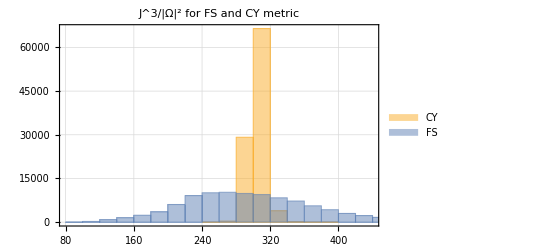

```mathematica
Histogram[{weightsCY,weightsFS},PlotLabel->"J^3/|Ω|^2 for FS and CY metric",PlotTheme->"Detailed",ChartLegends->{"CY", "FS"}]
```

To actually access the CY metric, we just call CYMetric on some points

```mathematica
{metrics, session}=CYMetric[{{1,2,3,4,5}},"Dir"->outDir]; (*NOTE: The code does not check whether the point is actually on the CY*)
```

```mathematica
{metrics, session}=CYMetric[pts,"Dir"->outDir];
```

```mathematica
metrics[[1,2]]//Chop//MatrixForm
```

(0.101153-1.28394×10^-9 ⅈ | 0.0345411-0.0168695 ⅈ | -0.0152393+0.0528888 ⅈ
0.0345411+0.0168695 ⅈ | 0.0936917-2.05346×10^-10 ⅈ | -0.0285692+0.036054 ⅈ
-0.0152393-0.0528888 ⅈ | -0.0285692-0.036054 ⅈ | 0.117389-1.86694×10^-9 ⅈ)

### Plot losses

```mathematica
history
```

<|sigma_loss→{0.276239,0.131117,0.12118,0.112184,0.10709,0.105608,0.104396,0.103393,0.102326,0.101874,0.101265,0.100113,0.0992199,0.0966265,0.0943799,0.0910961,0.0888292,0.0874477,0.0853012,0.0826078,0.0800652,0.0767183,0.0739524,0.0712059,0.0691495,0.0670579,0.0655088,0.0644098,0.0631226,0.0626533,0.061412,0.0610019,0.0600221,0.0594921,0.0589717,0.0586901,0.0582699,0.0576996,0.057751,0.0571748,0.0570162,0.0564565,0.0565229,0.0560303,0.0554945,0.0551588,0.0552435,0.05501,0.0541584,0.0539409,0.0537051,0.0531601,0.0528486,0.052526,0.0517133,0.0508847,0.0503235,0.0495523,0.0484515,0.0479191,0.0462837,0.0450137,0.0433366,0.0416001,0.0395072,0.0379383,0.0358897,0.0341683,0.0330365,0.0317388,0.0309687,0.0299477,0.029508,0.0290039,0.0281011,0.0273627,0.0272926,0.0266893,0.0264553,0.0256632,0.025405,0.0255062,0.0249747,0.0249015,0.0243512,0.0245877,0.0240529,0.0239946,0.0235407,0.0233573,0.0231957,0.0230374,0.0228107,0.0223993,0.0228247,0.0222739,0.0221298,0.022281,0.022051,0.0217162},kaehler_loss→{0.0050846,0.00179227,0.00277239,0.00428949,0.00348333,0.00334912,0.00339791,0.0032811,0.00332882,0.00332011,0.00328766,0.00332067,0.00324472,0.0032591,0.00330055,0.00334469,0.00329242,0.00310356,0.00283965,0.00253774,0.00220146,0.00193521,0.00177654,0.00172828,0.00166776,0.00157142,0.00151284,0.00145709,0.0014115,0.00139594,0.00138189,0.00135809,0.0013362,0.00132419,0.00132388,0.00131034,0.00130424,0.00130737,0.00131263,0.00130471,0.0012964,0.00129373,0.00130416,0.00130273,0.00128934,0.00128412,0.00130354,0.00132291,0.00133214,0.00133642,0.00134812,0.0013621,0.00136931,0.00139319,0.00141676,0.00144127,0.00147288,0.0015274,0.00158839,0.00164156,0.00172177,0.00180524,0.00186574,0.00191163,0.001978,0.00201728,0.00206073,0.00207203,0.0020728,0.00206161,0.0020408,0.00203166,0.00202464,0.00201084,0.0019924,0.00198377,0.00196674,0.00195152,0.0019451,0.00192734,0.00194548,0.00193453,0.00191667,0.00190623,0.00191139,0.00190058,0.0018951,0.0019079,0.00189217,0.00189539,0.00188858,0.0018911,0.00190803,0.00189735,0.00189018,0.0018909,0.00189502,0.00187589,0.00188518,0.00188526},transition_loss→{0.00446128,0.00547895,0.00577466,0.00372636,0.00192175,0.00156235,0.00152782,0.00149488,0.00149803,0.00151002,0.00153857,0.00159201,0.00167304,0.00180281,0.00197515,0.00207311,0.00205483,0.00197249,0.00189798,0.00178812,0.00166079,0.00154531,0.00149035,0.00145317,0.00142477,0.00136054,0.00130871,0.00124641,0.00119644,0.00115376,0.00111674,0.00108189,0.00105378,0.00102887,0.00103333,0.00100994,0.0010074,0.00100277,0.000998957,0.00099099,0.00098631,0.000989388,0.000992075,0.000994121,0.000991859,0.000994424,0.00100435,0.00101031,0.00101802,0.00101996,0.00102501,0.00103497,0.00104942,0.00105331,0.0010733,0.00108188,0.00110374,0.00112703,0.00115405,0.00116908,0.00118232,0.00120449,0.00121975,0.00121439,0.00121449,0.00118912,0.00118457,0.00115768,0.00112024,0.00109591,0.00105949,0.00103578,0.00100399,0.000973536,0.00094812,0.000933461,0.000905455,0.000884764,0.000873673,0.00084769,0.000831248,0.000822001,0.000808221,0.000795347,0.000790166,0.000775602,0.000769341,0.000770818,0.000755381,0.000759875,0.000749732,0.000740273,0.000745175,0.000731899,0.000733707,0.00072495,0.000718785,0.000721161,0.000723856,0.00071409},volk_loss→{0.0000185006,0.0000169899,0.0000170684,0.0000170655,0.0000171696,0.0000172541,0.0000172229,0.0000172549,0.00001721,0.000017246,0.0000172441,0.0000172205,0.0000172226,0.0000171823,0.0000170509,0.0000169616,0.0000168676,0.0000168228,0.0000167991,0.0000167417,0.0000166681,0.0000166409,0.0000165453,0.000016473,0.0000164354,0.0000163978,0.0000163565,0.0000163466,0.0000163392,0.0000163148,0.0000163413,0.0000162878,0.0000163013,0.0000162854,0.0000162926,0.0000162614,0.0000162622,0.000016249,0.0000162553,0.0000162631,0.0000162364,0.0000162372,0.0000162549,0.0000162584,0.0000162339,0.000016218,0.0000162018,0.0000162161,0.0000162244,0.0000162224,0.0000162064,0.000016182,0.0000161756,0.0000161504,0.0000161642,0.0000161625,0.0000161603,0.000016155,0.0000161254,0.0000161102,0.0000160966,0.0000160662,0.0000160484,0.000016031,0.0000160067,0.0000159754,0.0000159639,0.0000159568,0.0000159519,0.0000159363,0.0000159242,0.0000159261,0.0000159124,0.0000159088,0.0000159033,0.0000159002,0.0000159267,0.0000158968,0.0000158977,0.0000159015,0.0000159156,0.0000159159,0.0000159138,0.0000159029,0.000015896,0.0000158864,0.0000159073,0.0000159161,0.0000159074,0.0000158907,0.0000158953,0.0000158893,0.0000158945,0.0000158982,0.0000159033,0.0000158981,0.0000158946,0.0000159036,0.0000158949,0.0000158892},sigma_val→{0.132618,0.126574,0.120189,0.117777,0.11085,0.116656,0.110491,0.114094,0.110529,0.110404,0.111742,0.108965,0.109426,0.106348,0.100783,0.101491,0.09786,0.0994101,0.0946132,0.0923059,0.0922926,0.0834516,0.0807467,0.0782379,0.0782094,0.0745024,0.0723814,0.0729305,0.0744477,0.0695484,0.0682484,0.0679292,0.0685062,0.067602,0.0680022,0.066216,0.0654608,0.0668877,0.0656359,0.0668786,0.0655423,0.06737,0.0669652,0.0626631,0.0630649,0.0612073,0.0619408,0.0598314,0.0615701,0.0607915,0.05889,0.060233,0.0608747,0.0597464,0.0585503,0.0585274,0.0565082,0.0553178,0.054237,0.0542666,0.0512216,0.0488158,0.0452974,0.0476096,0.0422849,0.0390415,0.0351447,0.0347768,0.0325672,0.03584,0.0330474,0.0310764,0.0299617,0.0287288,0.0270392,0.0280228,0.0271651,0.0280905,0.0265842,0.0284284,0.0250386,0.0253389,0.0248874,0.0256098,0.0261554,0.0274399,0.0235215,0.0264328,0.025118,0.0243348,0.0233957,0.0228413,0.0223344,0.0222287,0.0207783,0.0236427,0.024352,0.0253977,0.0216226,0.0229959},kaehler_val→{0.00191458,0.00172016,0.00469209,0.00409824,0.00364364,0.00445776,0.00297411,0.00408544,0.00325601,0.00338411,0.00320878,0.00306966,0.00344444,0.00352097,0.00323409,0.00335936,0.00324422,0.00311958,0.00268514,0.00217019,0.00190549,0.00184771,0.00169945,0.0017269,0.00169869,0.00152267,0.00151819,0.00139222,0.001311,0.00139337,0.00139309,0.00139024,0.00136327,0.00135495,0.00133015,0.00123529,0.00133267,0.00133423,0.00131259,0.00120439,0.00122313,0.00124928,0.00124116,0.00128817,0.00131676,0.00131755,0.00129609,0.0014002,0.00136038,0.00131561,0.00134822,0.00131491,0.00134151,0.00137453,0.00140618,0.00137101,0.00144038,0.00164776,0.00151971,0.00159496,0.00176812,0.00196552,0.00181677,0.00201909,0.00198513,0.00196598,0.00204211,0.00217994,0.00201432,0.00202136,0.00203924,0.00198404,0.00200569,0.00197898,0.00200874,0.00191618,0.001984,0.00197601,0.00194282,0.00192893,0.00193893,0.00189514,0.00185825,0.001841,0.00181084,0.00186276,0.0018735,0.00177559,0.001829,0.00188702,0.00186799,0.00193662,0.0018392,0.00194481,0.00186691,0.00186415,0.0019568,0.00196625,0.00195352,0.00196399},transition_val→{0.00518396,0.00582342,0.00522151,0.00249516,0.00163828,0.00172774,0.00143788,0.00161767,0.00145756,0.00155178,0.00156177,0.00155782,0.00174669,0.00191431,0.00203102,0.00195446,0.00200052,0.00202036,0.00182482,0.00169478,0.00153851,0.00153578,0.0014101,0.00141893,0.00139357,0.00132266,0.00133131,0.00118954,0.00111709,0.00111297,0.00107086,0.00108235,0.00104723,0.00100436,0.00104094,0.00095563,0.00101828,0.0010019,0.000989163,0.000982858,0.000994499,0.000929783,0.000945054,0.000965266,0.00101542,0.000984213,0.000997883,0.00101528,0.00100656,0.00100682,0.0010065,0.00105423,0.00101528,0.00103291,0.00105311,0.00105895,0.00113119,0.00113244,0.00118444,0.00110021,0.00116615,0.0012358,0.00115797,0.00118941,0.00115778,0.00118361,0.00116735,0.00114601,0.00108061,0.00105822,0.00106574,0.00102698,0.000984193,0.000938566,0.000928965,0.000899985,0.00087806,0.000868391,0.000857338,0.000832281,0.000809119,0.000780891,0.000781568,0.00078454,0.000769284,0.00076071,0.000748271,0.000734623,0.000751921,0.000764642,0.000744283,0.0007436,0.000713869,0.000738142,0.000695706,0.000722059,0.000734352,0.000732878,0.000720938,0.000737795},ricci_val→{0.253967,0.234779,0.221288,0.16376,0.166761,0.180633,0.143914,0.168979,0.147664,0.162007,0.158063,0.14023,0.148778,0.14317,0.145147,0.137767,0.137185,0.155622,0.120083,0.11117,0.0997784,0.106796,0.0953296,0.093637,0.103228,0.0764127,0.0985382,0.0848635,0.0732771,0.0813894,0.0789397,0.0818996,0.083986,0.0770797,0.0755323,0.069864,0.0770842,0.0716518,0.0797565,0.0754635,0.0762023,0.0708844,0.0729345,0.070995,0.0762044,0.0761129,0.0708901,0.0784767,0.0669782,0.075284,0.07047,0.0755669,0.0691249,0.0708649,0.0744917,0.0708435,0.077861,0.0727573,0.0739563,0.07263,0.0694538,0.0714271,0.0746675,0.0726077,0.0710689,0.0745405,0.0723058,0.0676364,0.0688292,0.0583085,0.0690066,0.0596226,0.0566107,0.0576125,0.055391,0.053028,0.0506702,0.0501771,0.0496149,0.0484198,0.0475172,0.0479069,0.0446564,0.0448261,0.0457536,0.0424499,0.0406042,0.0447742,0.0420108,0.0391784,0.0410414,0.0431822,0.0398599,0.0371334,0.038028,0.0405538,0.0404785,0.0371199,0.0372108,0.0366966},volk_val→{0.921767,0.943779,0.974536,0.913933,1.00055,0.957843,0.938275,0.943747,0.948204,0.970916,0.978589,0.91249,0.925568,0.929081,0.961604,0.990463,0.994544,0.967785,0.972821,0.973625,0.926078,0.937852,0.996147,0.967877,1.00988,0.94507,0.985495,0.985772,0.937195,0.963185,0.981604,0.981045,0.973478,0.972463,0.976069,0.940754,0.973334,0.958183,1.00287,0.998064,0.990777,0.992952,0.997134,0.977547,0.982419,0.985779,0.970728,0.994794,0.946813,1.00139,0.968672,0.98528,0.982491,0.977682,0.986583,0.993515,1.00767,0.984843,0.993539,0.990562,0.972394,0.961366,0.984788,0.987016,0.999125,0.999013,0.994796,1.00785,0.996325,0.972879,1.01323,1.01465,0.99725,0.985724,0.999779,1.00808,0.985468,0.996342,0.994468,0.992119,1.00953,1.01555,0.990888,0.991842,1.00013,0.995655,0.987586,1.0118,1.00793,0.988265,0.994033,1.0005,0.995995,0.982785,0.992516,0.997654,1.00126,0.999321,0.983595,0.987949}|>

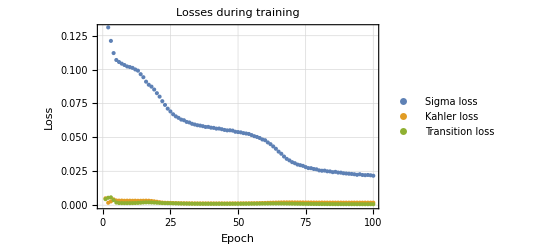

```mathematica
ListPlot[{history[["sigma_loss"]],history[["kaehler_loss"]],history[["transition_loss"]]},PlotLabel->"Losses during training",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

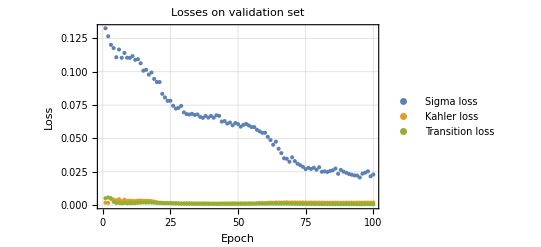

```mathematica
ListPlot[{history[["sigma_val"]],history[["kaehler_val"]],history[["transition_val"]]},PlotLabel->"Losses on validation set",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Kahler loss","Transition loss"},PlotTheme->"Detailed"]
```

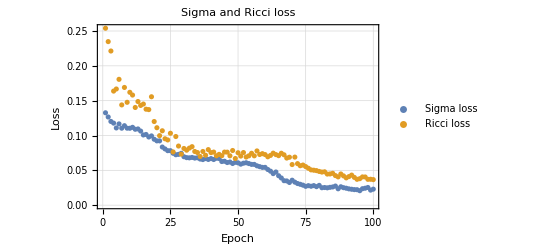

```mathematica
ListPlot[{history[["sigma_val"]],history[["ricci_val"]]},PlotLabel->"Sigma and Ricci loss",AxesLabel->{"Epoch","Loss"},PlotLegends->{"Sigma loss", "Ricci loss"},PlotTheme->"Detailed"]
```

```mathematica
SigmaVsRicci=Table[{history[["sigma_val"]][[i]],history[["ricci_val"]][[i]]},{i,Length[history[["sigma_val"]]]}];
```

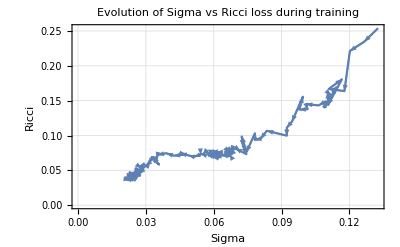

```mathematica
Show@@Join[{ListLinePlot[SigmaVsRicci,PlotLabel->"Evolution of Sigma vs Ricci loss during training",AxesLabel->{"Sigma","Ricci"},PlotTheme->"Detailed"]},Table[ListLinePlot[SigmaVsRicci[[i;;i+1]],PlotStyle->Directive[Thick,Arrowheads[.035]]]/.Line->Arrow,{i,Length[SigmaVsRicci]-1}]]
```

### Look at eigenvalues of the metric

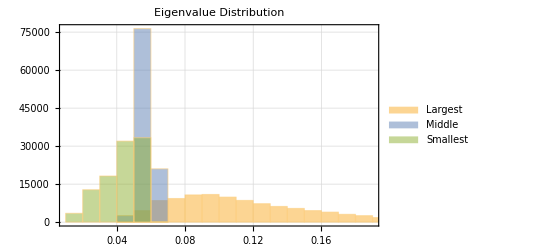

```mathematica
EigVals=Table[Eigenvalues[metrics[[i,2]]]//Re//Chop,{i,Length[metrics]}];
Histogram[{EigVals[[;;,1]],EigVals[[;;,2]],EigVals[[;;,3]]},PlotLabel->"Eigenvalue Distribution",PlotTheme->"Detailed",ChartLegends->{"Largest", "Middle","Smallest"}]
```